# Report Project 3

Course code: IX1500
Date: 2018-10-24

Rikard Jakobsson, rikjak@kth.se

Task 1: Dijkstra

## Summary

### Task

a) Explain how Dijkstra’s algorithm works. Use Mathematica graph-methods to illustrate your explanation with an animation.

### Result

Dijskstra’s algorithm finds the shortest path between two vertices in a graph by using a version of a breath first search. You start by marking the distance to all nodes directly reachable from the start node in a list, and setting the rest to infinity. You then add the reachable ones to a priority queue. For each element in the priotity queue you check its adjacent nodes. If the distance to one of these is bigger than the current distance plus the distance there from the current node you update it and add the current node as the ‘parent’ to the node looked at. When this is done you can recursively get the shortest path to a node from teh start node.

## Road Construction

### Model for cross section area

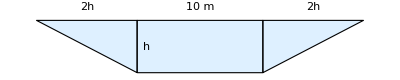

The given trapezoid area is

a(h)=(10+2h)h

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

The data is interpolated as a function A(x).

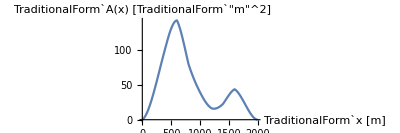

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Code

```mathematica
g = Graph[{1->2,1->6,1->3,2->4,2->5,4->5,4->6,5->8,3->7,7->3,3->1}];
g2 = Graph[{"a"->"b","a"->"f","a"->"c","b"->"d","b"->"e","d"->"e","d"->"f","e"->"h","c"->"g"}];
FindShortestPath[g2,"a","h"];
HighlightGraph[g,PathGraph[FindShortestPath[g,1,8,Method->"Dijkstra"],DirectedEdges->True]];
distance = {};
parent = {};
dijkstra[graph_,from_,to_]:= (parent = ConstantArray[0,Length[VertexList[graph]]];
distance =ConstantArray[Infinity,Length[VertexList[graph]]];
adjacent = MatrixForm[AdjacencyMatrix[graph]];
parent[[from]] =from;
distance[[from]] = 0;
visited{};
);
dijkstra[g,1,8];
distance
parent
adjacent
adjacent[[2]][[0]]
```

{0,∞,∞,∞,∞,∞,∞,∞}

{1,0,0,0,0,0,0,0}

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

Part::partw: Part 2 of SparseArray[Automatic,{8,8},0,{1,{{0,3,5,5,7,9,10,10,11},{{2},{3},{4},{5},{6},{1},{8},{3},{6},{7},{4}}},{1,1,1,1,1,1,1,1,1,1,1}}] does not exist.

Part